Special unitary particle pusher for extreme fields

DF Gordon, B Hafizi, Computer Physics Communications 258 (2021) 107628
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Prove equation 4->3

```mathematica
(* prove equation 4 implies equation 3 *)
Clear[ζ,u0,u1,u2,u3]
ζ={{u0+u3,u1-I u2},{u1+I u2,u0-u3}}
{0.5Tr[PauliMatrix[1].ζ],0.5Tr[PauliMatrix[2].ζ],0.5Tr[PauliMatrix[3].ζ]}//Simplify
```

{{u0+u3,u1-ⅈ u2},{u1+ⅈ u2,u0-u3}}

{1. u1,1. u2,1. u3}

## Prove equation 6

eq5: ζ(s+Δs)=Λ(Δs) ζ(s) Λ^†(Δs)
define generator λ through: Λ(Δs) =1+λ Δs
Replace in eq5: ζ(s+Δs)=(1+λ Δs) ζ(s) (1+λ^† Δs) = λ ζ(s) Δs + ζ(s) λ^†Δs + λ ζ(s) λ^†Δs^2
dζ/ds = (ζ(s+Δs)-ζ(s))/Δs = λ ζ(s) + ζ(s) λ^† + O(Δs) = λ ζ + ζ λ^†

## Prove equation 9

```mathematica
Clear[Ε,Εx,Εy,Εz,Β,Βx,Βy,Βz,Ω,e,m,c,σ,Ωnrm,Λ9,Λ,Δs]
Ε={Εx,Εy,Εz};
Β={Βx,Βy,Βz};
σ={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
(* eq8 *)
Ω=e/(2m c)(Ε+I Β);
(* eq7 *)
λ=σ[[1]]Ω[[1]]+σ[[2]]Ω[[2]]+σ[[3]]Ω[[3]];
(* eq10 *)
Ωnrm=Refine[Sqrt[Ω.Ω]//Simplify,{m>0,c>0,e>0}];
(*Ωnrm=Refine[Norm[Ω]//Simplify,{m>0,c>0,e>0}];*)
(* eq11 *)
ω=Ω/Ωnrm;

(* matrix exponential form of Λ*)
Λ=MatrixExp[λ Δs];
(* eq9 form of Λ *)
Λ9=IdentityMatrix[2]Cosh[Ωnrm Δs]+(λ/Ωnrm)Sinh[Ωnrm Δs]//Simplify;

(* choose random values for fields and physical parameters *)
{Εx,Εy,Εz}=RandomReal[{-1,+1},3];
{Βx,Βy,Βz}=RandomReal[{-1,+1},3];
c=RandomReal[];
m=RandomReal[];
e=RandomReal[];
Δs=RandomReal[{0,0.2}];
Λ9-Λ//Simplify//N//Chop
```

{{0,0},{0,0}}

```mathematica
(* Ψ.Ψ=0 for a PW *)
Clear[Ε,Εx,Εy,Εz,Β,Βx,Βy,Βz,Ω,e,m,c,σ,Ωnrm,Λ9,Λ,Ε0,Δs]
Ε={Εx,Εy,Εz};
Β={Βx,Βy,Βz};
{Εx,Εy,Εz}={0,Ε0,0};
{Βx,Βy,Βz}={0,0,Ε0};
σ={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
Ω=e/(2m c)(Ε+I Β);
Ψ=Ω Δs;
Ψ.Ψ
```

0

```mathematica
(* Ψ.Ψ = (σ.Ψ)^2 only for E^2-B^2=0 and E.B=0*)
Clear[Ε,Εx,Εy,Εz,Β,Βx,Βy,Βz,Ω,e,m,c,σ,Ωnrm,Λ9,Λ,Ε0,ΨΨ,Ψσ2,Δs]
Ε={Εx,Εy,Εz};
Β={Βx,Βy,Βz};
σ={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
Ω=e/(2m c)(Ε+I Β);
Ψ=Ω Δs;
ΨΨ=(Ψ[[1]]Ψ[[1]]+Ψ[[2]]Ψ[[2]]+Ψ[[3]]Ψ[[3]])//Simplify;
Ψσ2=(Ψ[[1]]σ[[1]]+Ψ[[2]]σ[[2]]+Ψ[[3]]σ[[3]]).(Ψ[[1]]σ[[1]]+Ψ[[2]]σ[[2]]+Ψ[[3]]σ[[3]]);
ΨΨ-Ψσ2//Expand//Simplify
```

{{0,(e^2 Δs^2 (-Βx^2-Βy^2-Βz^2+2 ⅈ Βx Εx+Εx^2+2 ⅈ Βy Εy+Εy^2+2 ⅈ Βz Εz+Εz^2))/(4 c^2 m^2)},{(e^2 Δs^2 (-Βx^2-Βy^2-Βz^2+2 ⅈ Βx Εx+Εx^2+2 ⅈ Βy Εy+Εy^2+2 ⅈ Βz Εz+Εz^2))/(4 c^2 m^2),0}}

```mathematica
(* Sqrt[Ψ.Ψ] is real for pure electric field -> Lorentz boost *)
Clear[Ε,Εx,Εy,Εz,Β,Βx,Βy,Βz,Ω,e,m,c,σ,Ωnrm,Λ9,Λ,Ε0,sqΨΨ,Ψσ2,Δs]
Ε={Εx,Εy,Εz};
Β={0,0,0};
σ={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
Ω=e/(2m c)(Ε+I Β);
Ψ=Ω Δs;
sqΨΨ=Refine[Sqrt[(Ψ[[1]]Ψ[[1]]+Ψ[[2]]Ψ[[2]]+Ψ[[3]]Ψ[[3]])//Simplify],{c>0,m>0,e>0,Εx∈Reals,Εy∈Reals,Εz∈Reals,Δs>0}]
```

(e Δs √(Εx^2+Εy^2+Εz^2))/(2 c m)

```mathematica
(* Sqrt[Ψ.Ψ] is imaginary for pure magnetic field -> rotation *)
Clear[Ε,Εx,Εy,Εz,Β,Βx,Βy,Βz,Ω,e,m,c,σ,Ωnrm,Λ9,Λ,Ε0,sqΨΨ,Ψσ2,Δs]
Ε={0,0,0};
Β={Βx,Βy,Βz};
σ={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
Ω=e/(2m c)(Ε+I Β);
Ψ=Ω Δs;
sqΨΨ=Refine[Sqrt[(Ψ[[1]]Ψ[[1]]+Ψ[[2]]Ψ[[2]]+Ψ[[3]]Ψ[[3]])//Simplify],{c>0,m>0,e>0,Βx∈Reals,Βy∈Reals,Βz∈Reals,Δs>0}]
```

(e √(-Βx^2-Βy^2-Βz^2) Δs)/(2 c m)

## Prove equation 19 ...

```mathematica
Clear[Ε,Εx,Εy,Εz,Β,Βx,Βy,Βz,Ω,e,m,c,σ,Ωnrm,Λ9,Λ,Δs,Ψσ,ΨΨ]
Ε={Εx,Εy,Εz};
Β={Βx,Βy,Βz};
σ={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
(* eq8 *)
Ω=e/(2m c)(Ε+I Β);
(* eq7 *)
λ=σ[[1]]Ω[[1]]+σ[[2]]Ω[[2]]+σ[[3]]Ω[[3]];
(* eq10 *)
Ωnrm=Refine[Sqrt[Ω.Ω]//Simplify,{m>0,c>0,e>0}];
(*Ωnrm=Refine[Norm[Ω]//Simplify,{m>0,c>0,e>0}];*)
(* eq11 *)
ω=Ω/Ωnrm;
Ψ=Ω Δs;
Ψσ=(Ψ[[1]]σ[[1]]+Ψ[[2]]σ[[2]]+Ψ[[3]]σ[[3]]);
ΨΨ=(Ψ[[1]]Ψ[[1]]+Ψ[[2]]Ψ[[2]]+Ψ[[3]]Ψ[[3]])//Simplify;

(* Λ(n) equation 17 *)
Λn=(1+Ψσ/2).Inverse[1-Ψσ/2]//Simplify;
(* eq19 form of Λ *)
Λ19=(1+Ψσ+ΨΨ/4)/(1-ΨΨ/4)//Simplify;

(* choose random values for fields and physical parameters *)
{Εx,Εy,Εz}=RandomReal[{-1,+1},3];
{Βx,Βy,Βz}=RandomReal[{-1,+1},3];
c=RandomReal[];
m=RandomReal[];
e=RandomReal[];
Δs=RandomReal[{0,0.2}];
Det[Λn]
Det[(1+Ψσ/2)]-Det[(1-Ψσ/2)]
Λn-Λ19//Simplify//N//Chop
```

-1.01609+0.0110517 ⅈ

0.0098092-0.0295714 ⅈ

{{0.955963+0.11057 ⅈ,-1.95288-0.116914 ⅈ},{1.97862+0.0757111 ⅈ,-2.94004-0.122202 ⅈ}}

## Prove equation 24

```mathematica
(* prove equation 24: trucate equation 23 at order s^2, solve for s as function of Δt, Taylor expand *)
Clear[Δs,t,Δt,eEu,m,c,u0]
Refine[Series[Solve[Δt==u0 s + eEu/(2 m c) s^2,s][[2,1,2]],{Δt,0,2}]//Simplify,{m>0,c>0,u0>0}]
```

Δt/u0-(eEu Δt^2)/(2 (c m u0^3))+O[Δt]^3

## Figure 1...

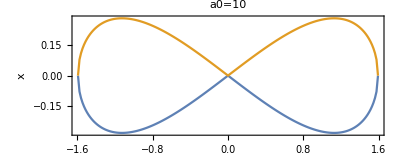

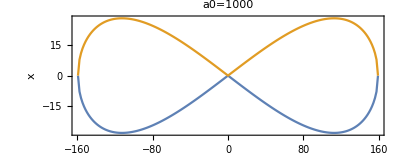

```mathematica
Clear[ω0,λ,c,a0,ωp,ρpll,ρprp,tab010,tab100]
ωp=ω0/Sqrt[1+0.5 a0^2];
ρpll=c/(8ωp)a0^2/(1+0.5 a0^2);
ρprp=c/ωp a0/Sqrt[1+0.5 a0^2];
λ=1;
c=1;
ω0=2π c/λ;

tab010={ParallelTable[{y,-2ρpll Sqrt[(y/ρprp)^2-(y/ρprp)^4]},{y,-ρprp,+ρprp,ρprp/100}],ParallelTable[{y,+2ρpll Sqrt[(y/ρprp)^2-(y/ρprp)^4]},{y,-ρprp,+ρprp,ρprp/100}]}/.{a0->10};
ListPlot[tab010,Joined->True,Frame->True,FrameLabel->{"y","x"},PlotLabel->"a0=10",AspectRatio->0.4]

tab100={ParallelTable[{y,-2ρpll Sqrt[(y/ρprp)^2-(y/ρprp)^4]},{y,-ρprp,+ρprp,ρprp/100}],ParallelTable[{y,+2ρpll Sqrt[(y/ρprp)^2-(y/ρprp)^4]},{y,-ρprp,+ρprp,ρprp/100}]}/.{a0->1000};
ListPlot[tab100,Joined->True,Frame->True,FrameLabel->{"y","x"},PlotLabel->"a0=1000",AspectRatio->0.4]
```